# Higgs to diphoton via a stop loop - attempt 1 with the FeynArts pipeline

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
<<FeynArts`
<<FormCalc`
```

FeynArts 3.10 (11 Jul 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

## Diagram Creation

> Top. 1 ad/becf/dedfef.m, 1 diagram

> Top. 2 ad/bece/dede.m, 1 diagram

> Top. 3 ad/becd/eded.m, 1 diagram

> Top. 4 ad/bdce/eded.m, 1 diagram

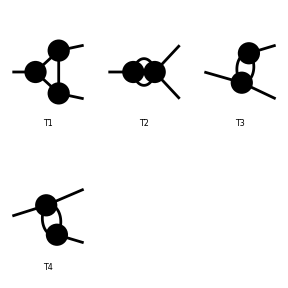

```mathematica
topo1=CreateTopologies[1,1->2,ExcludeTopologies->{Internal}];
Paint[topo1];
```

loading generic model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/MSSM.mod

> 94 particles (incl. antiparticles) in 23 classes

> $CounterTerms are ON

> 383 vertices

classes model {MSSM} initialized

Excluding 0 Generic, 31 Classes, and 74 Particles fields

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 0 Generic, 31 Classes, and 74 Particles fields

Restoring 18 field point(s)

in total: 3 Particles insertions

> Top. 1 ad/becf/dedfef.m, 2 diagrams

> Top. 2 ad/bece/dede.m, 1 diagram

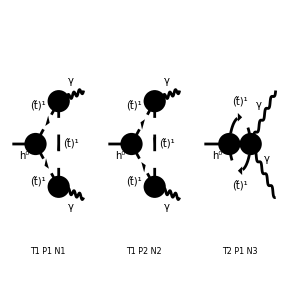

```mathematica
diag1=InsertFields[topo1,{S[1]}->{V[1],V[1]},InsertionLevel->{Particles},Model->"MSSM",
ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2],S[11],S[12],S[13,{1,1}],S[13,{2,1}],S[13,{1,2}],S[13,{2,2}],S[13,{2,3}],S[14],S[3],S[4],S[5],S[6],F[11],F[12],F[3],U[1],U[2],U[3],U[4]},Restrictions->NoLightFHCoupling];
Paint[diag1];
```

## Generate Amplitude

```mathematica
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag1],FermionChains->Chiral]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 1 Particles amplitude

in total: 3 Particles amplitudes

preparing FORM code in /home/paul/projects/physics/Research/fc-amp-1.frm

running FORM...

ok

Amp[{{S[1],k[1],Mh0,{}}}→{{V[1],k[2],0,{}},{V[1],k[3],0,{}}}][-1/(CW MW π SB SW)Alfa EL Sub5 (Pair1 (1/9 B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]-4/9 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]])-4/9 Pair2 Pair3 (C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]))]

#### Check divergent piece

```mathematica
UVDivergentPart[amp]
divergence=%[[1]]
```

Amp[{{S[1],k[1],Mh0,{}}}→{{V[1],k[2],0,{}},{V[1],k[3],0,{}}}][0]

0

#### Prepare for looptools

Note: polarization sum auto squares the matrix element

```mathematica
mat=PolarizationSum[amp,GaugeTerms->False]//.Subexpr[]//.Abbr[]//Simplify
```

HelicityME::nomat: Warning: No matrix elements to compute.

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /home/paul/projects/physics/Research/fc-pol-5.frm

running FORM...

ok

-1/(81 CW2 MW2 π SB2 SW2)8 Alfa Alfa2 (-(B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]-4 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]-2 Mh02 (C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]])) (B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]^*-4 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*)-2 Mh02 (-B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]+4 (C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+Mh02 (C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]))) (C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]^*)) (((6 CA CW MT2+MW MZ SAB SB (-3+4 SW2)) USf[1,1,3,3]+3 CW MT (MUEC SA+CA Af[3,3,3]) USf[1,2,3,3]) USfC[1,1,3,3]+(3 CW MT (MUE SA+CA AfC[3,3,3]) USf[1,1,3,3]+6 CA CW MT2 USf[1,2,3,3]-4 MW MZ SAB SB SW2 USf[1,2,3,3]) USfC[1,2,3,3]) (USf[1,2,3,3] (3 CW MT (MUEC SA+CA Af[3,3,3]) USfC[1,1,3,3]+6 CA CW MT2 USfC[1,2,3,3]-4 MW MZ SAB SB SW2 USfC[1,2,3,3])+USf[1,1,3,3] ((6 CA CW MT2+MW MZ SAB SB (-3+4 SW2)) USfC[1,1,3,3]+3 CW MT (MUE SA+CA AfC[3,3,3]) USfC[1,2,3,3]))

## Numerical Evaluation

```mathematica
Install["LoopTools"]
```

LinkObject[…]

```mathematica
VALUES[stopMass1_,stopMass2_,xt_,mu_,alpha_,beta_]:={
Den[p2_,m2_]:>1/(p2-m2),
MT->173,MT2->173^2,
MW->80.4,MW2->80.4^2,
MZ-> 91.2,MZ2-> (91.2)^2,
Mh0-> 125,Mh02->(125)^2,
Alfa->1/128,Alfa2->1/128^2,
SW2->0.2228,CW-> (MW/MZ),CW2->(MW/MZ)^2,
α-> alpha,β-> beta,MUE-> mu,
CA->Cos[α],SB->Sin[β],SA->Sin[α],
SB2->(Sin[β])^2,SAB->Sin[α+β],
thetat-> (1/2)(ArcSin[(-2*MT*xt)/(stopMass2^2-stopMass1^2)]),
MSf[1,3,x_]->stopMass1,MSf2[1,3,x_]->stopMass1^2,
MSf[2,3,x_]->stopMass2,MSf2[2,3,x_]->stopMass2^2,
Af[3,3,3]-> ((xt/(MT))+MUE*Cot[β]),AfC[3,3,3]-> ((xt/(MT))+MUE*Cot[β]),
USfC[x_,y_,3,3]-> USf[x,y,3,3],USf[1,1,3,3]->Cos[thetat] ,USf[1,2,3,3]->Sin[thetat]}
MyMatrixElement[stopMass1_,stopMass2_,xt_,mu_,alpha_,beta_]:=mat//.VALUES[stopMass1,stopMass2,xt,mu,alpha,beta]//Simplify
```

Reminder: This is the matrix element squared and summed

```mathematica
feynArtsResult =MyMatrixElement[250,10000,0,250,-0.1008,1.47]
```

0.000127552

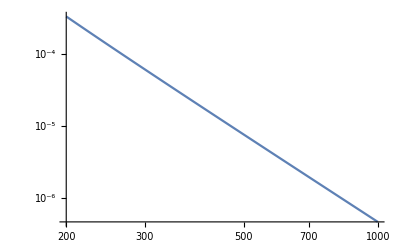

```mathematica
LogLogPlot[{MyMatrixElement[ms,10000,0,250,0,1.47]},{ms,200,1000}]
```

## Definitions and terminology

Notation for the diphoton decay:
p1= Momentum of 1st out-going particle (Z or photon)
p2= Momentum of 2nd out-going particle (photon)
mh= Mass of the decaying higgs
m = Mass of the stop
ghss= Higgs-stop coupling
α = Fine structure constant
x and y are Feynman parameters

Additional notation for the Zγ decay:
m1= Mass of the lighter stop mass eignestate
m2= Mass of the heavier stop mass eigenstate
zij= Coupling of the Z boson to stops of mass eigenstates ij = 11, 12, 21, 22
zgij= 4 point coupling of the Z boson and a photon to the stop mass eigenstates
hij= Higgs coupling to stops in their mass eigenstates (note: h11= ghSS)

After introducing all LO and NLO coefficients in this language, I will introduce the explicit dependence of these factors on MSSM parameters. See my summary Latex document for more details.

## Higgs to diphoton (on-shell)

```mathematica
matSq =Times[Rational[9,2],Plus[Times[Power[c2,2],Plus[Power[mg1,4],Times[Power[mg1,2],Plus[Times[4,Power[mg2,2]],Times[-2,Power[mh,2]]]],Power[Plus[Power[mg2,2],Times[-1,Power[mh,2]]],2]]],Times[6,c1,c2,Plus[Power[mg1,2],Power[mg2,2],Times[-1,Power[mh,2]]],Power[mZ,2]],Times[8,Power[c1,2],Power[mZ,4]]],Power[v,-2]](*Colour factors and polarization sums have already been taken into consideration - see matrix element squared file for details*)
```

(9 (c2^2 (mg1^4+mg1^2 (4 mg2^2-2 mh^2)+(mg2^2-mh^2)^2)+6 c1 c2 (mg1^2+mg2^2-mh^2) mZ^2+8 c1^2 mZ^4))/(2 v^2)

The c1 on-shell term is zero.

```mathematica
c2LOggInted = 2*(Rational[1, 18]*e^2*ghSS*v*
     (mh^2 - 4*m^2*ArcTan[mh*1/Sqrt[4*m^2 - mh^2]]^2))/(mh^4*Pi^2)
```

(e^2 ghSS v (mh^2-4 m^2 ArcTan[mh/(√(4 m^2-mh^2))]^2))/(9 mh^4 π^2)

## Coupling definitions

Explicitly, we can write out these couplings in terms of MSSM parameters - for more details see my summary Latex document.

#### Z couplings

```mathematica
z11=-(e/(2*sW*cW))*(ct^2 - 4sW^2/3)
```

-(e (ct^2-(4 sW^2)/3))/(2 cW sW)

```mathematica
z22=-(e/(2*sW*cW))*(st^2 - 4sW^2/3)
```

-(e (st^2-(4 sW^2)/3))/(2 cW sW)

```mathematica
z12=(e/(2*sW*cW))*(ct*st)
```

(ct e st)/(2 cW sW)

Within these expressions, e is the elementary charge, s_W and c_W are the sine and cosine of the Weinberg angle, and c_t is the cosine of the stop mixing angle.

#### Z-γ couplings

```mathematica
zg11=(2e^2/(3*sW*cW))*(ct^2 - 4sW^2/3)
```

(2 e^2 (ct^2-(4 sW^2)/3))/(3 cW sW)

```mathematica
zg22=(2e^2/(3*sW*cW))*(st^2 - 4sW^2/3)
```

(2 e^2 (st^2-(4 sW^2)/3))/(3 cW sW)

```mathematica
zg12=-(2e^2/(3*sW*cW))*(ct*st)
```

-(2 ct e^2 st)/(3 cW sW)

#### Higgs couplings

```mathematica
h11= a*ct^2 +b*st^2 +2*c*ct*st
```

a ct^2+2 c ct st+b st^2

```mathematica
h22 = a*st^2 +b*ct^2 -2*c*ct*st
```

b ct^2-2 c ct st+a st^2

```mathematica
h12= -a*ct*st +b*ct*st +c*(ct^2-st^2)
```

-a ct st+b ct st+c (ct^2-st^2)

Where we have (in the decoupling limit)

```mathematica
a=-(e*mt^2/(mW*sW))-(e*mZ/(cW*sW))Cos[2β](1/2 -2*sW^2/3)
```

-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW)

```mathematica
b=-(e*mt^2/(mW*sW))-(e*mZ/(cW*sW))Cos[2β](2*sW^2/3)
```

-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW)

```mathematica
c = ((e*mt)/(2*mW*sW))(At-μ*Cot[β])
```

(e mt (At-μ Cot[β]))/(2 mW sW)

μ and β  are your standard MSSM paramters, m_t is the mass of the top, and A_t is a soft breaking term that can be expressed in terms of the stop mixing parameter and μ.

```mathematica
SUBIN[stopMass1_,stopMass2_,xt_,mu_,beta_]:={
mt->173,
mW->80.4,
mZ-> 91.2,
mh-> 125,
Alfa->1/128,Alfa2->(1/128)^2,
sW->0.4720,cW-> (mW/mZ),
β-> beta,μ-> mu,
thetat-> (1/2)(ArcSin[(-2*mt*xt)/(stopMass2^2-stopMass1^2)]),
e-> Sqrt[(4*Pi*Alfa)],
m->stopMass1,
At-> ((xt)+μ*Cot[β]),
ct->Cos[thetat] ,st->Sin[thetat]}
MyResults[stopMass1_,stopMass2_,xt_,mu_,beta_]:=matToSub//.SUBIN[stopMass1,stopMass2,xt,mu,beta]//Simplify
```

## Plug in values and compare to FeynArts result

```mathematica
c1 = 0;
c2 =c2LOggInted//. ghSS-> h11
```

(e^2 v (mh^2-4 m^2 ArcTan[mh/(√(4 m^2-mh^2))]^2) (st^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+ct^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))+(ct e mt st (At-μ Cot[β]))/(mW sW)))/(9 mh^4 π^2)

```mathematica
matSq
```

1/(18 mh^8 π^4)e^4 (mg1^4+mg1^2 (4 mg2^2-2 mh^2)+(mg2^2-mh^2)^2) (mh^2-4 m^2 ArcTan[mh/(√(4 m^2-mh^2))]^2)^2 (st^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+ct^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))+(ct e mt st (At-μ Cot[β]))/(mW sW))^2

```mathematica
osMatSq = matSq /. mg1 -> 0 /. mg2 -> 0
```

(e^4 (mh^2-4 m^2 ArcTan[mh/(√(4 m^2-mh^2))]^2)^2 (st^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+ct^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))+(ct e mt st (At-μ Cot[β]))/(mW sW))^2)/(18 mh^4 π^4)

```mathematica
myCalcResult = %//.SUBIN[250,10000,0,250,1.47]//Simplify
```

0.000127561

```mathematica
myCalcResult/feynArtsResult
```

1.00007

# Check the Carena paper directly

```mathematica
matElementSqu = (Alfa2*mh^4/(32*Pi^2))*((numC*qs^2*ghSS/m^2)*aloop)^2
```

(Alfa2 aloop^2 ghSS^2 mh^4 numC^2 qs^4)/(32 m^4 π^2)

```mathematica
ScalarLoop[x_] := -x(1-x*ArcSin[Sqrt[1/x]]^2)
```

```mathematica
tauS = 4*m^2/mh^2
```

(4 m^2)/mh^2

```mathematica
aloop =ScalarLoop[tauS]//.mt-> 173//.mh->125//.m-> 250.//Simplify
```

0.344912

```mathematica
matElementSqu//.SUBIN[250,10000,0,250,1.47]//Simplify
```

1.4369×10^-9 ghSS^2 numC^2 qs^4

```mathematica
%/.ghSS-> h11 /. numC-> 3/.qs-> (2/3)
```

2.55449×10^-9 (st^2 (-(e mt^2)/(mW sW)-(2 e mZ sW Cos[2 β])/(3 cW))+ct^2 (-(e mt^2)/(mW sW)-(e mZ (1/2-(2 sW^2)/3) Cos[2 β])/(cW sW))+(ct e mt st (At-μ Cot[β]))/(mW sW))^2

```mathematica
carenaCalcResult = %//.SUBIN[250,10000,0,250,1.47]//Simplify
```

0.000127561

```mathematica
carenaCalcResult/myCalcResult
```

1.

```mathematica
carenaCalcResult/feynArtsResult
```

1.00007